Radiation Reaction Cooling as a Source of Anisotropic Momentum Distributions with Inverted Populations

P. J. Bilbao and L. O. Silva, Phys. Rev. Lett. 130, 165101 (2023)
Link: https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.130.165101
Notebook: Óscar Amaro, October 2023 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

## Eq 5 Method of characteristics

```mathematica
Clear[t,pprp,ppll,f,f0,α,B0,γ]

(* the ansatz for the method of characteristics in eq 4 *)
f=f0[x,y]/(2/3 α B0 pprp t-1)^4

(* these will be the characteristic arguments of the distribution function, which will be the original one evaluated with updated momenta *)
x=pprp/(1-2/3 α B0 pprp t);
y=ppll/(1-2/3 α B0 pprp t);
γ=pprp;

(* the definition of f will automatically satisfy eq4. trying an f0 function with a different combination of arguments will in general not satisfy that equation *)
D[f,pprp]//Simplify;

(* PDE of equation 4 *)
(3/(2α B0)D[f,t]-(4 pprp^2/γ f+pprp^3/γ D[f,pprp]+(pprp^2 ppll)/γ D[f,ppll])//Simplify)
```

f0[pprp/(1-2/3 B0 pprp t α),ppll/(1-2/3 B0 pprp t α)]/(-1+2/3 B0 pprp t α)^4

0

## Evolution of ring radius - Figure 2

```mathematica
(* for early times, the ring radius grows linearly *)
Clear[t,pR,pth,τ,B0,α,m,ωce,B,e,c,tt]
τ = 2 α B0 t/3;
pR = (1+6pth^2 τ^2-Sqrt[1+12pth^2 τ^2])/(6 pth^2 τ^3);
Series[pR,{t,0,2}]
```

2 B0 pth^2 α t+O[t]^3

```mathematica
(* for late times, the ring radius decays as  *)
Clear[t,pR,pth,τ,B0,α,m,ωce,B,e,c,tt]
τ = 2 α B0 t/3;
pR = (1+6pth^2 τ^2-Sqrt[1+12pth^2 τ^2])/(6 pth^2 τ^3);
Asymptotic[pR,t->∞]//Normal
```

3/(2 B0 t α)

```mathematica
(* maximum value of ring until it starts decreasing, equation 8 *)
Clear[t,pR,pth,τ,B0,α,m,ωce,B,e,c,tt]
τ = 2 α B0  t/(3);
pR = (1+6pth^2 τ^2-Sqrt[1+12pth^2 τ^2])/(6 pth^2 τ^3);
(* turning point time*)
Solve[(D[pR,t]//Simplify)==0,t]
(* maximum radius *)
pR/.{t->3/(4 B0 pth α)}
```

{{t→-3/(4 B0 pth α)},{t→3/(4 B0 pth α)}}

(2 pth)/3

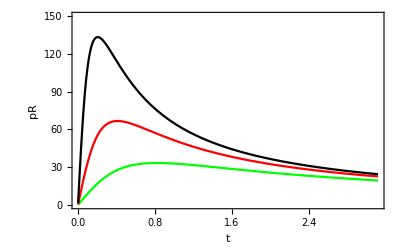

```mathematica
(* full evolution *)
Clear[t,pR,pth,τ,B0,α,m,ωce,B,e,c,tt]
B0=2.5;
c=3 10^8;
m=9.11 10^-31;
e = 1.6 10^-19;
α=1/137;
ωce = e B0/m;
τ = 2 α B0  t/(3);
3/(4 B0 pth α) ωce 10^-6;
pR = (1+6pth^2 τ^2-Sqrt[1+12pth^2 τ^2])/(6 pth^2 τ^3)//Simplify;
Plot[{pR/.{pth->50},pR/.{pth->100},pR/.{pth->200}},{t,10^-3,3.12},PlotRange->{0,150},Frame->True,PlotStyle->{Green,Red,Black},FrameLabel->{"t","pR"}]
```